```mathematica
Clear["Global`*"]
```

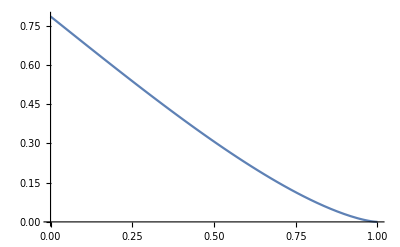

```mathematica
Plot[1/2*a^2*ArcCos[r/a]-1/2*r*Sqrt[a^2-r^2]/.a->1,{r,0,1}]
```

```mathematica
a=14;
d=14*Sqrt[2]
```

14 √2

```mathematica
b1[u_,v_]:=Piecewise[{{1/2*a^2*ArcCos[Sqrt[u^2+v^2]/a]-1/2*Sqrt[u^2+v^2]*Sqrt[a^2-u^2-v^2],u^2+v^2<a^2},{0,u^2+v^2≥a^2}}]
```

```mathematica
b2[u_,v_]:=Piecewise[{{1/2*a^2*ArcCos[Sqrt[(u-d)^2+v^2]/a]-1/2*Sqrt[(u-d)^2+v^2]*Sqrt[a^2-(u-d)^2-v^2],(u-d)^2+v^2<a^2},{0,(u-d)^2+v^2≥a^2}}]
```

```mathematica
NIntegrate[b1[u,v]*b2[u,v],{u,-a,a+d},{v,-a,a}]
```

29502.9

```mathematica
c0=1.6766292047202967*^6;
c14=271051.3566266247;
c20=29502.92261374786;
```

```mathematica
c14/c0
```

0.161664